```mathematica
(*This just rewrites a whole mess of variables from a Mathematica notation to a Matlab notation*)
varreplace=Flatten@{{Nx[x,y,z]->Nx,Ny[x,y,z]->Ny,Nz[x,y,z]->Nz,Table[D[Nx[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dNxd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[Ny[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dNyd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[Nz[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dNzd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],Table[D[Nx[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2Nxd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}],Table[D[Ny[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2Nyd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}],Table[D[Nz[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2Nzd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}]},{Nx[x,y]->Nx,Ny[x,y]->Ny,Table[D[Nx[x,y],{x,y}⟦ii⟧]->ToExpression["dNxd"<>ToString[{x,y}⟦ii⟧]],{ii,2}],
Table[D[Ny[x,y],{x,y}⟦ii⟧]->ToExpression["dNyd"<>ToString[{x,y}⟦ii⟧]],{ii,2}],Table[D[Nx[x,y],{x,y}⟦ii⟧,{x,y}⟦jj⟧]->ToExpression["d2Nxd"<>ToString[{x,y}⟦ii⟧]<>"d"<>ToString[{x,y}⟦jj⟧]],{ii,2},{jj,2}],Table[D[Ny[x,y],{x,y}⟦ii⟧,{x,y}⟦jj⟧]->ToExpression["d2Nyd"<>ToString[{x,y}⟦ii⟧]<>"d"<>ToString[{x,y}⟦jj⟧]],{ii,2},{jj,2}]},Flatten@{θ[x,y,z]->θ,ϕ[x,y,z]->ϕ,Table[D[θ[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dθd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[ϕ[x,y,z],{x,y,z}⟦ii⟧]->ToExpression["dϕd"<>ToString[{x,y,z}⟦ii⟧]],{ii,3}],
Table[D[θ[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2θd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}],Table[D[ϕ[x,y,z],{x,y,z}⟦ii⟧,{x,y,z}⟦jj⟧]->ToExpression["d2ϕd"<>ToString[{x,y,z}⟦ii⟧]<>"d"<>ToString[{x,y,z}⟦jj⟧]],{ii,3},{jj,3}]},Flatten@{ϕ[x,y]->ϕ,
Table[D[ϕ[x,y],{x,y}⟦ii⟧]->ToExpression["dϕd"<>ToString[{x,y}⟦ii⟧]],{ii,2}],
Table[D[ϕ[x,y],{x,y}⟦ii⟧,{x,y}⟦jj⟧]->ToExpression["d2ϕd"<>ToString[{x,y}⟦ii⟧]<>"d"<>ToString[{x,y}⟦jj⟧]],{ii,2},{jj,2}]},α[x,y,z]->a,β[x,y,z]->b};
```

```mathematica
(*Download this package online.*)
Needs["ToMatlab`"]
```

Needs::nocont: Context "ToMatlab`" was not created when Needs was evaluated.

We want to find the minimum energy configuration for a 2D or 3D cell of liquid crystal. We first need to define an energy function. There are two candidates: the Oseen-Frank model and the Q-tensor model. The first is empirical, easily visualized, and simpler. The second is more accurate but a bit more complicated. The energy to be minimized is an integral in 2D or 3D. Like Lagrangian mechanics, in which we minimize an action that is an integral of the Lagrangian over time, we need to minimize the free energy functional that is an integral of the free energy over space. To do so, we can use the Euler-Lagrange equations:
https://en.wikipedia.org/wiki/Euler–Lagrange_equation
The integration variables are x, y, and z instead of t.

Begin by defining the director in a chosen coordinate system. Remember that the director is a vector field. We can define it using Cartesian or spherical coordinates, and define it on a Cartesian or spherical grid. I am restricting to a Cartesian grid here. You would need to be careful with your derivatives and integral on a spherical grid. Spherical coordinates are preferred to define the director itself because they can easily preserve normalization.

```mathematica
(*A few options here. Uncomment your choice and evaluate the whole notebook. It may take a while for the 3D cases, especially with saddlesplay. In each case, we define the n vector as well as the functions to be solved for (the q(t)'s) in the wikipedia page. Each of these functions depend on x, y, and z on the Cartesian grid.*)

(*3D Cartesian:*)
(*n:={Nx[x,y,z],Ny[x,y,z],Nz[x,y,z]}
funcs:={Nx[x,y,z],Ny[x,y,z],Nz[x,y,z]}
fgS := -Ws*({Wx, Wy, Wz}.n)^2*)

(*2D Cartesian*)
(*n:={Nx[x,y],Ny[x,y],0}
funcs:={Nx[x,y],Ny[x,y]}*)
(*fgS=-Ws ({Bx,By,Bz}.n)^2;*)

(*3D Spherical*)
n:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}/.{θ->θ[x,y,z]0+π/2,ϕ->ϕ[x,y,z]}
funcs:={θ[x,y,z],ϕ[x,y,z]}
fgS := -Ws*({Sin[α]Cos[β],Sin[α]Sin[β], Cos[α]}.n)^2 /. {α->α[x,y,z], β->β[x,y,z]}

(*2D Polar*)
(*n:={Cos[ϕ],Sin[ϕ],0}/.{ϕ->ϕ[x,y]}
funcs:={ϕ[x,y]}
fgS:= -Ws*({Cos[α],Sin[α],0}.n)^2/.{α-> α[x,y]}*)
```

```mathematica
(*Levi-civita tensor in a more convenient form:*)
ϵ=Normal@LeviCivitaTensor[3];
```

Following H. Mori, E. C. Gartland, J. R. Kelly, and P. J. Bos, Jpn. J. Appl. Phys. 38, 135 (1999), we write down the free energy density in the Q-tensor representation. Equations 4 & 5:

```mathematica
(*Functions to encode Equations 4 and 5. Q with 2 arguments will form the components of the Q-tensor (Eq. 4),and Q with 3 arguments will take the derivative of an element of the Q tensor with respect to a variable (Eq. 5).*)
Q[j_,k_]:=S/2(3 n⟦j⟧n⟦k⟧-KroneckerDelta[j,k])
Q[j_,k_,l_]:=D[Q[j,k],{x,y,z}⟦l⟧]
```

Equation 3. Einstein summation notation means that the repeated indices are summed over. For now, we will not need G_4^(2) (which accounts for cholesteric pitch).

```mathematica
G12=Sum[Q[j,k,l]Q[j,k,l],{j,3},{k,3},{l,3}]//Simplify;
G22=Sum[Q[j,k,k]Q[j,l,l],{j,3},{k,3},{l,3}]//Simplify;
G32=Sum[Q[j,k,l]Q[j,l,k],{j,3},{k,3},{l,3}]//Simplify;
G42=Sum[ϵ⟦j,k,l⟧Q[j,m]Q[k,m,l],{j,3},{k,3},{l,3},{m,3}]//Simplify;
G63=Sum[Q[j,k]Q[l,m,j]Q[l,m,k],{j,3},{k,3},{l,3},{m,3}]//Simplify;
```

Equation 13 (we aren’t doing anything with electric fields, thankfully). I am also ignoring the G_4^(2) term because q_0=0 for nematics.

```mathematica
(*Note the K24 saddle-splay term. Multiply it by 0 if you don't want it.*)
fgQ=Collect[Simplify[1/27(K33-K11+3K22)G12/S^2+2/9(K11-K22-K24)G22/S^2+2/9 G32/S^2 K24+2/27(K33-K11)G63/S^3 ],{K11,K22,K33,K24},Simplify](*/.{K22->K11,K33->K11,K24->K11}//FullSimplify*);
```

The Oseen-Frank formulation: https://en.wikipedia.org/wiki/Distortion_free_energy_density

```mathematica
bend:=1/2 K11 Div[n,{x,y,z}]^2//FullSimplify
twist:=1/2 K22(n.Curl[n,{x,y,z}])^2//FullSimplify
splay:=1/2 K33(Cross[n,Curl[n,{x,y,z}]].Cross[n,Curl[n,{x,y,z}]])//Simplify
Del={D[#,x],D[#,y],D[#,z]}&;
saddlesplay:=1/2 K24 Div[(n.Del[#]&)@n-n(Div[n,{x,y,z}]),{x,y,z}]//FullSimplify
(*saddlesplay=0;*)
(*Comment the saddle-splay back in if you choose.*)
fgOF=bend+twist+splay+saddlesplay;
```

```mathematica
(*Pick which form of the free energy to use, including the surface energy if you so choose (scaled by factor Ws). The surface energy applies an energy bonus for aligned with the preferred direction notated by the unit vector {Bx,By,Bz}. Feel free to define this in spherical coordinates or whatever.*)
(*fgS=-Ws ({Bx,By,Bz}.n)^2;*)

(*use this line to switch between Oseen Frank and Q tensor representations*)
(*fg=fgOF + fgS;*)
fg = fgOF + fgS;
```

```mathematica
(*View the free energy and copy to Matlab form if needed.*)
fg;
StringReplace[FullSimplify[fg /.{K11->K,K22->K,K33->K,K24->K}]//.varreplace   //ToMatlab,{"ϕ"->"np","θ"->"nt"}]
```

(1/2).*((dnpdx.^2+dnpdy.^2+dnpdz.^2).*K+(-2).*Ws.*cos(b+(-1).*np).^2.* ...
  sin(a).^2);

```mathematica
(*General form for Euler-Lagrange equations. Notice the intermittent Simplify's. This is a little quicker than simplifying only at the end. There is one equation for each function*)
ELeqs=Flatten@Table[
D[fg,funcs⟦ELii⟧]-Sum[Simplify@D[Simplify@Quiet@D[fg,Simplify@D[funcs⟦ELii⟧,{x,y,z}⟦ii⟧]],{x,y,z}⟦ii⟧],{ii,3}],{ELii,Length@funcs}]
```

{0,-2 Ws (Cos[ϕ[x,y,z]] Sin[α[x,y,z]] Sin[β[x,y,z]]-Cos[β[x,y,z]] Sin[α[x,y,z]] Sin[ϕ[x,y,z]]) (Cos[β[x,y,z]] Cos[ϕ[x,y,z]] Sin[α[x,y,z]]+Sin[α[x,y,z]] Sin[β[x,y,z]] Sin[ϕ[x,y,z]])-K22 ϕ^(0,0,2)[x,y,z]+(K11-K33) Sin[2 ϕ[x,y,z]] (ϕ^(0,1,0)[x,y,z])^2-(K11 Cos[ϕ[x,y,z]]^2+K33 Sin[ϕ[x,y,z]]^2) ϕ^(0,2,0)[x,y,z]+2 (K11-K33) Cos[2 ϕ[x,y,z]] ϕ^(0,1,0)[x,y,z] ϕ^(1,0,0)[x,y,z]-(K11-K33) Sin[2 ϕ[x,y,z]] (ϕ^(1,0,0)[x,y,z])^2+K11 (-Sin[ϕ[x,y,z]] ϕ^(0,1,0)[x,y,z]-Cos[ϕ[x,y,z]] ϕ^(1,0,0)[x,y,z]) (Cos[ϕ[x,y,z]] ϕ^(0,1,0)[x,y,z]-Sin[ϕ[x,y,z]] ϕ^(1,0,0)[x,y,z])+K33 (Sin[ϕ[x,y,z]] ϕ^(0,1,0)[x,y,z]+Cos[ϕ[x,y,z]] ϕ^(1,0,0)[x,y,z]) (Cos[ϕ[x,y,z]] ϕ^(0,1,0)[x,y,z]-Sin[ϕ[x,y,z]] ϕ^(1,0,0)[x,y,z])+(K11-K33) Sin[2 ϕ[x,y,z]] ϕ^(1,1,0)[x,y,z]-(K33 Cos[ϕ[x,y,z]]^2+K11 Sin[ϕ[x,y,z]]^2) ϕ^(2,0,0)[x,y,z]}

```mathematica
(*You now have an array that has the Euler-Lagrange equation for each of your variables (components of the director vector). Replace the number to view the EL equation for the corresponding variable.*)
funcs
```

{θ[x,y,z],ϕ[x,y,z]}

```mathematica
(*Check out the one constant approximation to see if it makes sense.*)
StringReplace[FullSimplify[ELeqs /.{K11->K,K22->K,K33->K,K24->K}]//.varreplace   //ToMatlab,{"ϕ"->"np","θ"->"nt"}]
```

[0,(-1).*(d2npdxdx+d2npdydy+d2npdzdz).*K+(-1).*Ws.*sin(a).^2.*sin(2.* ...
  (b+(-1).*np))];

```mathematica
(*Optional: rearrange the Euler-Lagrange equations such that each of the elastic constants appears once with its own term. This may or may not be shorter than the original expressions.*)
ELeqsSimp=Collect[#,{K11,K22,K33,K24},FullSimplify]&/@ELeqs;
```

```mathematica
ELeqsSimp⟦1⟧ /. varreplace //ToMatlab
```

0;

In the 2 D case with one constant approximation, the energy comes out looking like the Laplace equation. Mathematica has nice built in tools for solving such linear systems:

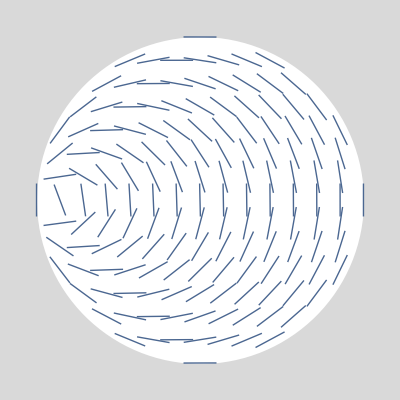

```mathematica
(*For a circular region, it likes to put the singularity at an edge.*)

region=Disk[];
sol=NDSolveValue[{∇_{x,y}^2 ϕ[x,y]==0,DirichletCondition[ϕ[x,y]==ArcTan[x, y]+π/2,x^2+y^2==1]},ϕ,{x,y}∈region];
Show[{Graphics[{White,region},Background->LightGray],Quiet@VectorPlot[Through[{Cos,Sin}[sol[x,y]]],{x,y}∈region,VectorStyle->Arrowheads[0]]}]
```

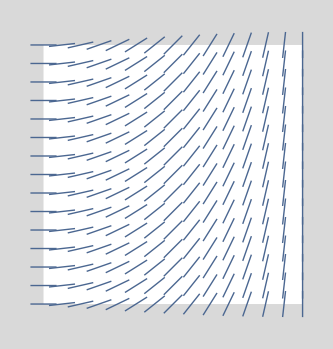

```mathematica
(*Here's a linear twist.*)
region2=Rectangle[];
sol2=NDSolveValue[{∇_{x,y}^2 ϕ[x,y]==0,DirichletCondition[ϕ[x,y]==0,x==0],DirichletCondition[ϕ[x,y]==π/2,x==1]},ϕ,{x,y}∈region2];
Show[{Graphics[{White,region2},Background->LightGray],Quiet@VectorPlot[Through[{Cos,Sin}[sol2[x,y]]],{x,y}∈region2,VectorStyle->Arrowheads[0]]}]
```

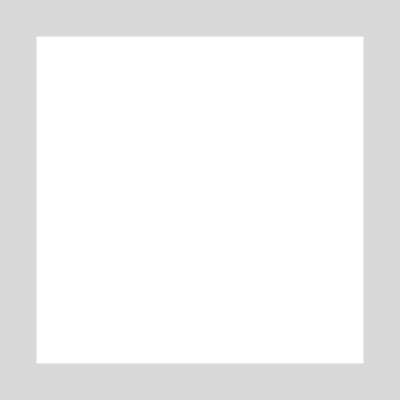
```mathematica
(*Show[{-Graphics-,VectorPlot[Through[{Cos,Sin}[sol2[x,y]]],{x,y}∈region2,VectorStyle->Arrowheads[0]]}]*)
```

```mathematica
varreplace]
```

```mathematica
{{Nx[x,y,z]->Nx}, {Ny[x,y,z]->Ny}, {Nz[x,y,z]->Nz}, {Derivative[1,0,0][Nx][x,y,z]->dNxdx}, {Derivative[0,1,0][Nx][x,y,z]->dNxdy}, {Derivative[0,0,1][Nx][x,y,z]->dNxdz}, {Derivative[1,0,0][Ny][x,y,z]->dNydx}, {Derivative[0,1,0][Ny][x,y,z]->dNydy}, {Derivative[0,0,1][Ny][x,y,z]->dNydz}, {Derivative[1,0,0][Nz][x,y,z]->dNzdx}, {Derivative[0,1,0][Nz][x,y,z]->dNzdy}, {Derivative[0,0,1][Nz][x,y,z]->dNzdz}, {Derivative[2,0,0][Nx][x,y,z]->d2Nxdxdx}, {Derivative[1,1,0][Nx][x,y,z]->d2Nxdxdy}, {Derivative[1,0,1][Nx][x,y,z]->d2Nxdxdz}, {Derivative[1,1,0][Nx][x,y,z]->d2Nxdydx}, {Derivative[0,2,0][Nx][x,y,z]->d2Nxdydy}, {Derivative[0,1,1][Nx][x,y,z]->d2Nxdydz}, {Derivative[1,0,1][Nx][x,y,z]->d2Nxdzdx}, {Derivative[0,1,1][Nx][x,y,z]->d2Nxdzdy}, {Derivative[0,0,2][Nx][x,y,z]->d2Nxdzdz}, {Derivative[2,0,0][Ny][x,y,z]->d2Nydxdx}, {Derivative[1,1,0][Ny][x,y,z]->d2Nydxdy}, {Derivative[1,0,1][Ny][x,y,z]->d2Nydxdz}, {Derivative[1,1,0][Ny][x,y,z]->d2Nydydx}, {Derivative[0,2,0][Ny][x,y,z]->d2Nydydy}, {Derivative[0,1,1][Ny][x,y,z]->d2Nydydz}, {Derivative[1,0,1][Ny][x,y,z]->d2Nydzdx}, {Derivative[0,1,1][Ny][x,y,z]->d2Nydzdy}, {Derivative[0,0,2][Ny][x,y,z]->d2Nydzdz}, {Derivative[2,0,0][Nz][x,y,z]->d2Nzdxdx}, {Derivative[1,1,0][Nz][x,y,z]->d2Nzdxdy}, {Derivative[1,0,1][Nz][x,y,z]->d2Nzdxdz}, {Derivative[1,1,0][Nz][x,y,z]->d2Nzdydx}, {Derivative[0,2,0][Nz][x,y,z]->d2Nzdydy}, {Derivative[0,1,1][Nz][x,y,z]->d2Nzdydz}, {Derivative[1,0,1][Nz][x,y,z]->d2Nzdzdx}, {Derivative[0,1,1][Nz][x,y,z]->d2Nzdzdy}, {Derivative[0,0,2][Nz][x,y,z]->d2Nzdzdz}, {Nx[x,y]->Nx}, {Ny[x,y]->Ny}, {Derivative[1,0][Nx][x,y]->dNxdx}, {Derivative[0,1][Nx][x,y]->dNxdy}, {Derivative[1,0][Ny][x,y]->dNydx}, {Derivative[0,1][Ny][x,y]->dNydy}, {Derivative[2,0][Nx][x,y]->d2Nxdxdx}, {Derivative[1,1][Nx][x,y]->d2Nxdxdy}, {Derivative[1,1][Nx][x,y]->d2Nxdydx}, {Derivative[0,2][Nx][x,y]->d2Nxdydy}, {Derivative[2,0][Ny][x,y]->d2Nydxdx}, {Derivative[1,1][Ny][x,y]->d2Nydxdy}, {Derivative[1,1][Ny][x,y]->d2Nydydx}, {Derivative[0,2][Ny][x,y]->d2Nydydy}, {θ[x,y,z]->θ}, {ϕ[x,y,z]->ϕ}, {Derivative[1,0,0][θ][x,y,z]->dθdx}, {Derivative[0,1,0][θ][x,y,z]->dθdy}, {Derivative[0,0,1][θ][x,y,z]->dθdz}, {Derivative[1,0,0][ϕ][x,y,z]->dϕdx}, {Derivative[0,1,0][ϕ][x,y,z]->dϕdy}, {Derivative[0,0,1][ϕ][x,y,z]->dϕdz}, {Derivative[2,0,0][θ][x,y,z]->d2θdxdx}, {Derivative[1,1,0][θ][x,y,z]->d2θdxdy}, {Derivative[1,0,1][θ][x,y,z]->d2θdxdz}, {Derivative[1,1,0][θ][x,y,z]->d2θdydx}, {Derivative[0,2,0][θ][x,y,z]->d2θdydy}, {Derivative[0,1,1][θ][x,y,z]->d2θdydz}, {Derivative[1,0,1][θ][x,y,z]->d2θdzdx}, {Derivative[0,1,1][θ][x,y,z]->d2θdzdy}, {Derivative[0,0,2][θ][x,y,z]->d2θdzdz}, {Derivative[2,0,0][ϕ][x,y,z]->d2ϕdxdx}, {Derivative[1,1,0][ϕ][x,y,z]->d2ϕdxdy}, {Derivative[1,0,1][ϕ][x,y,z]->d2ϕdxdz}, {Derivative[1,1,0][ϕ][x,y,z]->d2ϕdydx}, {Derivative[0,2,0][ϕ][x,y,z]->d2ϕdydy}, {Derivative[0,1,1][ϕ][x,y,z]->d2ϕdydz}, {Derivative[1,0,1][ϕ][x,y,z]->d2ϕdzdx}, {Derivative[0,1,1][ϕ][x,y,z]->d2ϕdzdy}, {Derivative[0,0,2][ϕ][x,y,z]->d2ϕdzdz}, {ϕ[x,y]->ϕ}, {Derivative[1,0][ϕ][x,y]->dϕdx}, {Derivative[0,1][ϕ][x,y]->dϕdy}, {Derivative[2,0][ϕ][x,y]->d2ϕdxdx}, {Derivative[1,1][ϕ][x,y]->d2ϕdxdy}, {Derivative[1,1][ϕ][x,y]->d2ϕdydx}, {Derivative[0,2][ϕ][x,y]->d2ϕdydy
α(x,y,z) -> a
β(x,y,z) -> b}}
```